## MOT Atom Number

```mathematica
ClearAll
```

Here I want to calculate from the MOT fluorescence measured by our PixelFly camera, the number of atoms in our MOT. f#=1.8, lens has a diameter of 25 10^-3 m and is placed about 0.19 m away from the source. Quantum efficiency 0.24%

```mathematica
collectedFraction=(aperture)^2/(16 Distance^2)/.{aperture->25*10^-3/1.8,Distance->0.19}
```

0.00033397

With the new system, we have the MOT illuminating a Lens 140mm aways with a diameter of 2 inches. The light then passes through a 200mm focal length lens to the Pixis camera. The quantum efficiency of the camera at 780nm is about 94%. Optical transmission of the lens is: 98% I looked at a tipical acromate lense on Edmond Optics, and they state reflectivity of around 0.75% per surface at 780nm. So I took it to be worse at 1% per surface.

```mathematica
collectedFraction=(aperture)^2/(16 Distance^2)/.{aperture->2*25.4*10^-3,Distance->0.14}
```

0.00822908

```mathematica
countsPerPhoton=0.74;
transmission=0.98; 
ndFilter = 10^-0.6;

expTime=3000 10^-6;
```

Calibration for Pixis camera

```mathematica
calibration=1/(collectedFraction transmission 0.24)
```

516.668

Calibration for Pixelfly camera

```mathematica
calibration=1/(collectedFraction transmission countsPerPhoton)
```

167.568

old 33269.8

```mathematica
objImg=2^16 ImageData[Import["/Users/paul/Data/University Stuff/CQT/images/140114_1657_56 MOT.tif"]];
```

```mathematica
image=Import["/Users/paul/Data/University Stuff/CQT/images/140114_1657_56 MOT.tif"]
```

```mathematica
bg=Mean[objImg[[10,All]]]
```

3103.44

Estimate image background and subtract

```mathematica
bg=Mean[objImg[[500,1;;200]]]
```

1082.64

```mathematica
image=objImg-bg;
```

```mathematica
ImageAdjust[Image[image[[450;;700,350;;650]]]]
```

-Graphics-

```mathematica
croppedImage=image[[450;;700,350;;650]];
```

```mathematica
ListContourPlot[croppedImage]
```

-Graphics-

```mathematica
integratedCounts=Total[Flatten[croppedImage]]
```

1.80409×10^8

```mathematica
totalIntensity = (38.6+39.9+41.1+37) 2.4;
```

```mathematica
rate=Γ/2 intensity/(1+4(Δ/Γ)^2+intensity)/.{Γ->2π 6.065 10^6,intensity->totalIntensity/2.54^2/3.5,Δ->-12 10^6}
```

1.75787×10^7

```mathematica
atoms=calibration/(rate expTime)integratedCounts
```

0.00317748 integratedCounts

```mathematica
sizeX=150*0.7*13 10^-3
```

1.365

```mathematica
sizeY=170 0.7 13 10^-3
```

1.547

```mathematica
100/3.5
```

28.5714

```mathematica
totalIntensity/2.54^2/3.5
```

16.6444

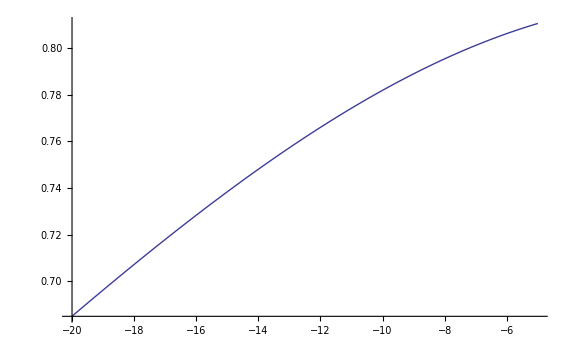

```mathematica
Plot[(int/ints)/(1+4(Δ/Γ)^2+int/ints)/.{ints->3.5,int->16,Γ->2π 6.065},{Δ,-20,-5}]
```

```mathematica
collectedFraction transmission countsPerPhoton rate Na Texp/.{Na->10^6,Texp->300 10^-6}
```

3.14715×10^7

```mathematica
collectedFraction transmission countsPerPhoton rate 10^6 10^-6/50^2
```

41.962

```mathematica
2^16
```

65536

```mathematica
42*300
```

12600